# PHYS 611, Fall 2025

## Theoretical Mechanics

## Homework Set 1. - TA Solution

Thomas (Tom) C. Gorordo

## 1. Damped oscillator

```mathematica
F = -m ω0^2 x[t] - m γ x'[t];
DHODE = m x''[t]== F
```

m x''[t]==-m ω0^2 x[t]-m γ x'[t]

### (a)

```mathematica
Xa[t_]:= Δ ⅇ^(ⅈ ω t);
DHODE/.{x->Xa}//Simplify
```

ⅇ^(ⅈ t ω) m Δ (-ⅈ γ ω+ω^2-ω0^2)==0

eliminating the common factor as nonzero, find a quadratic condition that:

```mathematica
CONDa = (-ⅈ γ ω+ω^2-ω0^2)==0;
```

### (b)

```mathematica
Solve[CONDa, ω]
```

{{ω→1/2 (ⅈ γ-√(-γ^2+4 ω0^2))},{ω→1/2 (ⅈ γ+√(-γ^2+4 ω0^2))}}

from which we can observe that solutions will be pure imaginary if

```mathematica
CONDb = -γ^2+4 ω0^2 <= 0;
```

### (c)

```mathematica
Xc[t_]:= ap ⅇ^(-kp t)+am ⅇ^(-km t)
```

Since we’re solving a 2nd order homogeneous ODE, we know we can form a general solution as a superposition of the two solutions found in (a), so we can specifically take

```mathematica
kp = -ⅈ ω/. Solve[CONDa, ω][[1]]//Expand
km = -ⅈ ω /.Solve[CONDa, ω][[2]]//Expand
```

γ/2+1/2 ⅈ √(-γ^2+4 ω0^2)

γ/2-1/2 ⅈ √(-γ^2+4 ω0^2)

where the condition found in (b) implies we are in an overdamped (or critically damped) regime.
We can check this indeed yields a solution:

```mathematica
DHODE/.{x->Xc}//Simplify
```

True

noticing that the second term in these expressions is the hinted at frequency parameter

```mathematica
ωw == 1/2 ⅈ √(-γ^2+4 ω0^2);
```

it will simplify our further manipulations to write

```mathematica
kp = γ/2+ωw;
km = γ/2-ωw;
```

### (d)

The Cauchy boundary conditions

```mathematica
CONDd = {x[0] == X0, x'[0] == V0};
```

imply coefficients

```mathematica
COEFFSd = Solve[CONDd/.{x->Xc},{ap, am}][[1]]//Expand
```

{ap→X0/2-V0/(2 ωw)-(X0 γ)/(4 ωw),am→X0/2+V0/(2 ωw)+(X0 γ)/(4 ωw)}

so the solution takes the form

```mathematica
Xd[t_]:= Xc[t]/.COEFFSd
```

```mathematica
Xd[t]
```

ⅇ^(t (-γ/2-ωw)) (X0/2-V0/(2 ωw)-(X0 γ)/(4 ωw))+ⅇ^(t (-γ/2+ωw)) (X0/2+V0/(2 ωw)+(X0 γ)/(4 ωw))

### (e)

```mathematica
Xe[t_]:=Limit[Xd[t],ωw->0]
Xe[t]
```

1/2 ⅇ^(-(t γ)/2) (2 t V0+2 X0+t X0 γ)

## 2. Why the harmonic oscillator is special

```mathematica
U[x_]:=A Abs[x]^n
```

### (a)

The turning points occur when the whole energy is potential

```mathematica
Xturn = x[t]/.Solve[EE == U[x[t]], x[t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{-(EE/A)^(1/n),(EE/A)^(1/n)}

```mathematica
xturn = Xturn[[2]]
```

(EE/A)^(1/n)

### (b)

T = ∫ⅆt = ∫ⅆt/ⅆx ⅆx

where

```mathematica
DEFb = 
EE == 1/2 m (x'[t])^2+Hold[U[x[t]]];
```

so dt/dx is

```mathematica
1/x'[t]/.Solve[DEFb, x'[t]][[2]]
```

(√m)/(√2 √(EE-Hold[U[x[t]]]))

thus, we aim to integrate

√(m/(2 EE))∫_Xturn[[1]]^Xturn[[2]] 1/(√(1-U[x[t]]/EE))ⅆx

breaking down the integral further, notice that

U[x[t]]/EE == U[x[t]]/U[xturn] == Abs[x[t]/xturn]^n

and the integral can be rewritten

√(m/(2EE))∫_0^xturn 1/(√1-Abs[x/xturn]^n)ⅆx

which is nondimensional under the substitution w = x / xturn

```mathematica
T= 2 Assuming[{n>0, n∈Integers}, xturn√(m/(2EE))∫_0^1 1/(√(1-u^n))ⅆu]
```

((EE/A)^(1/n) √(m/EE) √(2 π) Gamma[1+1/n])/Gamma[1/2+1/n]

```mathematica
2 Assuming[{n>0, n∈Integers}, ∫_0^1 1/(√(1-u^n))ⅆu]
```

(2 √π Gamma[1+1/n])/Gamma[1/2+1/n]

#### (c)

We didn’t need to evaluate the integral to do this next part, because it will vanish in a ratio:

```mathematica
1/T D[T,EE]//Simplify//Expand
```

-1/(2 EE)+1/(EE n)

## 3. Linear two-spring oscillator

### (a)

```mathematica
SOLa = Solve[0 == (m(x1[t] + x2[t]) + M X[t])/(2m + M),X[t]]
```

{{X[t]→-(m (x1[t]+x2[t]))/M}}

### (b)

```mathematica
EOM = m{{x1''[t]},{x2''[t]}}=={{-k, 0},{0, -k}}.{{x1[t]},{x2[t]}} + k{{X[t] - d},{X[t]+d}};
```

```mathematica
EOM/.SOLa//Expand
```

{{{m x1''[t]},{m x2''[t]}}=={{-d k-k x1[t]-(k m x1[t])/M-(k m x2[t])/M},{d k-(k m x1[t])/M-k x2[t]-(k m x2[t])/M}}}

### (c)

```mathematica
CONDc = EOM/.SOLa/.{x1''[t]->0, x2''[t]->0}//Simplify
```

{{{(k (d M+(m+M) x1[t]+m x2[t]))/M},{(k (-d M+m x1[t]+(m+M) x2[t]))/M}}=={{0},{0}}}

```mathematica
Solve[CONDc, {x1[t], x2[t]}]
```

{{x1[t]→-d,x2[t]→d}}

### (d)

```mathematica
Xd1[t_]:=a1 ⅇ^(ⅈ ω t)-d
Xd2[t_]:=a2 ⅇ^(ⅈ ω t)+d
```

Setting a1 = a2 = a

```mathematica
EOM/.SOLa/.{x1->Xd1, x2->Xd2}/.{a1->a,a2->a}//Simplify
```

{{{(a ⅇ^(ⅈ t ω) (k (2 m+M)-m M ω^2))/M},{(a ⅇ^(ⅈ t ω) (k (2 m+M)-m M ω^2))/M}}=={{0},{0}}}

we can read off a sufficient condition for the frequency of a nontrivial solution

```mathematica
Solve[(k (2 m+M)-m M ωp2) ==0, ωp2]
```

{{ωp2→(k (2 m+M))/(m M)}}

and the a1 = -a2 = a ansatz proceeds similarly

```mathematica
EOM/.SOLa/.{x1->X1, x2->X2}/.{a1->a,a2->-a}//Simplify
```

{{{m X1''[t]},{m X2''[t]}}=={{-(k (d M+(m+M) X1[t]+m X2[t]))/M},{k (d-X2[t]-(m (X1[t]+X2[t]))/M)}}}

```mathematica
Solve[ (k-m ωm2)==0,ωm2]
```

{{ωm2→k/m}}

```mathematica
wp2 = wm2 (2m + M)/M
```

((2 m+M) wm2)/M

### (e)

```mathematica
X1[t_]:= -d +am ⅇ^(ⅈ ωm t)+Conjugate[am] ⅇ^(-ⅈ ωm t)+ap ⅇ^(ⅈ ωp t)+Conjugate[ap] ⅇ^(-ⅈ ωp t)
X2[t_]:=d - am ⅇ^(ⅈ ωm t)-Conjugate[am] ⅇ^(-ⅈ ωm t)+ap ⅇ^(ⅈ ωp t)+Conjugate[ap] ⅇ^(-ⅈ ωp t)
```

```mathematica
CONDe = {X1[0]==-d,X2[0]==d,X1'[0]==0,X2'[0]==v}//Simplify
```

{am+ap+Conjugate[am]+Conjugate[ap]==0,am+Conjugate[am]==ap+Conjugate[ap],am ωm+ap ωp==ωm Conjugate[am]+ωp Conjugate[ap],-ⅈ (am ωm-ap ωp-ωm Conjugate[am]+ωp Conjugate[ap])==v}

```mathematica
X1[t]/.Solve[CONDe,{ap, am, Conjugate[ap], Conjugate[am]}]//ExpToTrig
X2[t]/.Solve[CONDe,{ap, am, Conjugate[ap], Conjugate[am]}]//ExpToTrig
```

{-d-(v Sin[t ωm])/(2 ωm)+(v Sin[t ωp])/(2 ωp)}

{d+(v Sin[t ωm])/(2 ωm)+(v Sin[t ωp])/(2 ωp)}

### (f)

```mathematica
SOLa/.{x1->X1,x2->X2}/.Solve[CONDe,{ap, am, Conjugate[ap], Conjugate[am]}]//ExpToTrig//Simplify
```

{{{X[t]→-(m v Sin[t ωp])/(M ωp)}}}

### (g)

```mathematica
(X2[t]-X1[t])/.Solve[CONDe,{ap, am, Conjugate[ap], Conjugate[am]}]//ExpToTrig//Simplify
```

{2 d+(v Sin[t ωm])/ωm}

where this frequency is smaller (see (d)).

### (h)

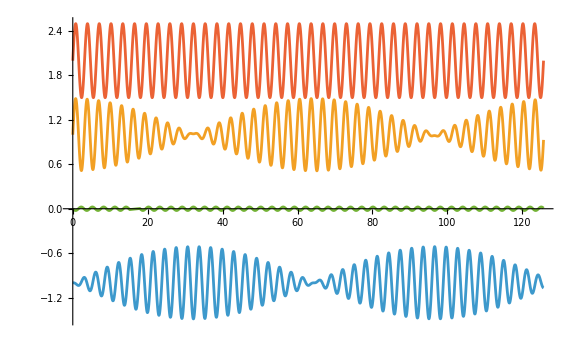

```mathematica
Plot[Evaluate[{
X1[t],
X2[t],
X[t]/.SOLa/.{x1->X1,x2->X2},
X2[t]-X1[t]}
/.Solve[CONDe,{ap, am, Conjugate[ap], Conjugate[am]}]
/.{ωp->ωm √((2m + M)/M)}/.{d->1,ωm->2, M->20m, v->1}//Simplify],
{t,0, 40π}, ImageSize->Large]
```

### (i)

```mathematica
X''[t]==D[X[t]/.SOLa,{t,2}]/.Solve[EOM,{x1''[t],x2''[t]}]/.Solve[X[t]==(X[t]/. SOLa),{x1[t]}]//Simplify
```

{{X''[t]=={-(k (2 m+M) X[t])/(m M)}}}

```mathematica
δX''[t]==D[x2[t]-x1[t],{t,2}]/.Solve[EOM,{x1''[t],x2''[t]}]/.{x2[t]->δX[t]+x1[t]}//Simplify
```

{δX''[t]==(k (2 d-δX[t]))/m}

whose frequencies are again seen to come from our physically intuited ansatz in (d).